```mathematica
Quit
```

```mathematica
PacletDirectoryLoad["~/github/lenia/Lenia"]
```

{/Users/arnoudb/github/lenia/Lenia}

```mathematica
Needs["Lenia`"]
```

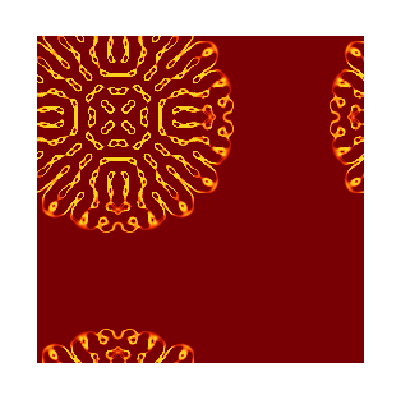

```mathematica
gridSize={256,256};R=13;
grid=N@Table[Module[{r=Sqrt[(i-64)^2+(j-64)^2]/R},If[r<1.0,Exp[-((r-0.5)^2)/(2*0.15^2)],0.0]],{i,256},{j,256}];
result=Lenia[grid,200,"Mu"->0.15,"Sigma"->0.015,"Radius"->R];
ArrayPlot[result,ColorFunction->"SolarColors"]
```

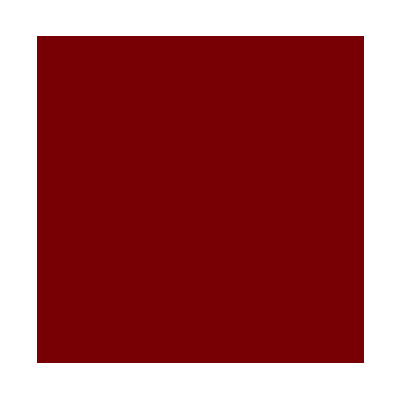

```mathematica
grid=LeniaBlob[{100,100},{50,50},5,0.5];
result=Lenia[grid,100,"Mu"->0.15,"Sigma"->0.015];
ArrayPlot[result,ColorFunction->"SolarColors"]
```

```mathematica
sz=256;
gridSize={sz,sz};
R=13;
grid=N@Table[Module[{r=Sqrt[(i-sz/2.0)^2+(j-sz/2.0)^2]/R},If[r<1.0,Exp[-((r-0.5)^2)/(2*0.15^2)],0.0]],{i,sz},{j,sz}];

history=Lenia[grid,200,"ReturnHistory"->True,"Radius"->R];

ListAnimate[ArrayPlot[#,ColorFunction->"SolarColors",Frame->False]&/@history]
```